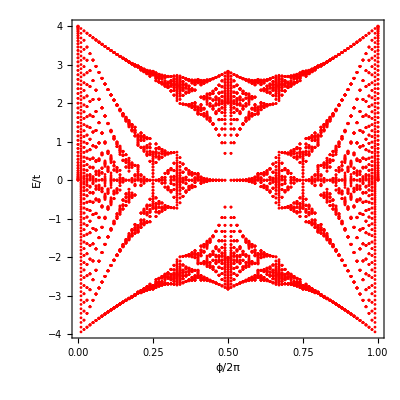

```mathematica
t[p_,q_]:=Table[If[i==j,2Cos[2.π i p/q],If[Mod[i-j,q]==1||Mod[j-i,q]==1,1,0]],{i,0,q-1},{j,0,q-1}];
hb=Table[{p/100,e},{p,0,100},{e,Eigenvalues[t[p,100]]}];
ListPlot[hb,PlotStyle->{{Red,PointSize[0.005]}},AspectRatio->1,Frame->True,FrameLabel->{"ϕ/2π","E/t"},Axes->False,FrameStyle->Black,LabelStyle->{20,FontFamily->Times}]
```